## Definitions

```mathematica
Clear[ac,le,lp,lu,ls,Qs,Qu,Z1,Z2,rmsp,rmsm,EISCOp,EISCOm]
```

```mathematica
(* Special values of a defined on Table 5 / Eq. (4.21) that are relevant to describe the root systems involving the ergosphere. *)
```

```mathematica
ac[1]:=1/Sqrt[2];ac[2]:=2(Sqrt[2]-1);ac[3]:=Sqrt[2(Sqrt[2]-1)];ac[4]:=2Sqrt[2]/3;ac[5]:=2Sqrt[Sqrt[5]-2];
ac[6]:=(2 √(9+7 √33-8 (3 (9+7 √33))^(1/3)))/(3 (9+7 √33))^(1/3);
```

```mathematica
(* Special values of the angular momentum defined on Eq. (2.18), Eq. (4.23), Eq. (4.39) and Eq. (4.40) that are relevant to describe the root systems involving the ergosphere. *)
```

```mathematica
lp[e_,a_]:=2 (1+Sqrt[1-a^2])/a e
le[e_,a_]:=((4+2a^2)e^2-a^2)/(2 a e)
lu[e_,a_]:=Module[{r,D},
r=Root[a^4-8 a^2 #1+(16+8 a^2-10 a^2 e^2) #1^2+(-32-2 a^2+24 e^2+6 a^2 e^2-4 a^2 e^4) #1^3+(24-32 e^2+9 e^4) #1^4+(-8+14 e^2-6 e^4) #1^5+(1-2 e^2+e^4) #1^6&,3];
If[Element[r,Reals] && r ≤2,
D=((r-3)r^(1/2)+2a); 
If[D≥0,(r^2-2a Sqrt[r]+a^2)/Sqrt[D]/r^(3/4)
]
]]
ls[e_,a_]:=Module[{r,D},
r=Root[a^4-8 a^2 #1+(16+8 a^2-10 a^2 e^2) #1^2+(-32-2 a^2+24 e^2+6 a^2 e^2-4 a^2 e^4) #1^3+(24-32 e^2+9 e^4) #1^4+(-8+14 e^2-6 e^4) #1^5+(1-2 e^2+e^4) #1^6&,4];
If[Element[r,Reals]&& r ≤2,
D=((r-3)r^(1/2)+2a);
If[D≥0,(r^2-2a Sqrt[r]+a^2)/Sqrt[D]/r^(3/4)
]
]]
```

```mathematica
(* Carter's constant leading to double roots as a function of (E,\ell) as defined in Eq. (3.59) and Eq. (3.60) *)
```

```mathematica
Qu[e_,L_,a_]:=Module[{r,root,thisroot},
root[1]=Root[a^4 e^2-2 a^3 e L+a^2 L^2+(-a^4+a^4 e^2-a^2 L^2) #1+(4 a^2-2 a^2 e^2+2 a e L) #1^2+(-4-2 a^2+2 a^2 e^2) #1^3+(4-3 e^2) #1^4+(-1+e^2) #1^5&,2];
root[2]=Root[a^4 e^2-2 a^3 e L+a^2 L^2+(-a^4+a^4 e^2-a^2 L^2) #1+(4 a^2-2 a^2 e^2+2 a e L) #1^2+(-4-2 a^2+2 a^2 e^2) #1^3+(4-3 e^2) #1^4+(-1+e^2) #1^5&,4];
 If[Re[root[1]]>Re[root[2]],thisroot=1,thisroot=2];
(a^2 e^2-2 a e L+L^2-a^2 r+a^2 e^2 r-L^2 r+3 r^2-2 r^3+2 e^2 r^3)/(-1+r)/.r-> root[thisroot]
]
Qs[e_,L_,a_]:=Module[{r,root,thisroot},
root[1]=Root[a^4 e^2-2 a^3 e L+a^2 L^2+(-a^4+a^4 e^2-a^2 L^2) #1+(4 a^2-2 a^2 e^2+2 a e L) #1^2+(-4-2 a^2+2 a^2 e^2) #1^3+(4-3 e^2) #1^4+(-1+e^2) #1^5&,3];
root[2]=Root[a^4 e^2-2 a^3 e L+a^2 L^2+(-a^4+a^4 e^2-a^2 L^2) #1+(4 a^2-2 a^2 e^2+2 a e L) #1^2+(-4-2 a^2+2 a^2 e^2) #1^3+(4-3 e^2) #1^4+(-1+e^2) #1^5&,5];
 If[Re[root[1]]>Re[root[2]],thisroot=1,thisroot=2];
(a^2 e^2-2 a e L+L^2-a^2 r+a^2 e^2 r-L^2 r+3 r^2-2 r^3+2 e^2 r^3)/(-1+r)/.r-> root[thisroot]
]
```

```mathematica
(* Definitions of energy at the ISCO prograde (EISCOp) and retrograde (EISCOm) equatorial Kerr orbits, Eqs. (3.27), (3.28), (3.29)
 *)
```

```mathematica
Z1[a_]:=1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3));
Z2[a_]:=Sqrt[3a^2+Z1[a]^2];
rmsp[a_]:= 3+Z2[a]-Sqrt[(3-Z1[a])(3+Z1[a]+2Z2[a])];
rmsm[a_]:=3+Z2[a]+Sqrt[(3-Z1[a])(3+Z1[a]+2Z2[a])];
EISCOp[a_]:=Module[{r},r=rmsp[a];((-2+r) r^3+a √(r^5))/(r^2 √((-3+r) r^3+2 a √(r^5)))]
EISCOm[a_]:=Module[{r},r=rmsm[a];((-2+r) r^3-a √(r^5))/(r^2 √((-3+r) r^3-2 a √(r^5)))]
```

## Figure 7

```mathematica
{EISCOp[0.5],EISCOm[0.5]}
```

{0.917882,0.954858}

```mathematica
(* No real solution in the range Q ≥ 0*)
```

```mathematica
Block[{a=1/2,e=0.90},Plot[{Qs[e,l,a],Qu[e,l,a]},{l,-4,4},PlotRange-> {{-9,8},{0,60}}]]
```

-Graphics-

```mathematica
(* We start to see it for E≥ EISCOp *)
```

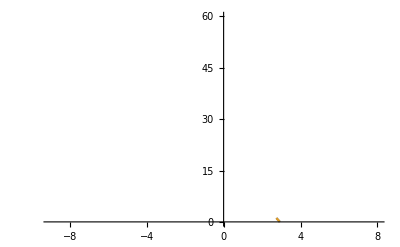

```mathematica
Block[{a=1/2,e=0.92},Plot[{Qs[e,l,a],Qu[e,l,a]},{l,-4,4},PlotRange->{{-9,8},{0,60}}]]
```

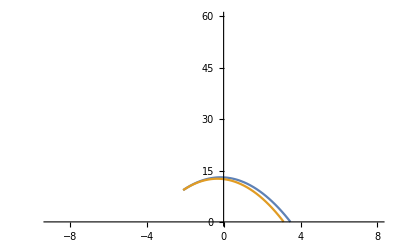

```mathematica
Block[{a=1/2,e=0.95},Plot[{Qs[e,l,a],Qu[e,l,a]},{l,-4,4},PlotRange->{{-9,8},{0,60}}]]
```

```mathematica
(* Now for  E≥ EISCOm we have two separate parabolas:  *)
```

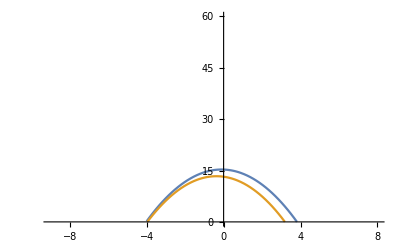

```mathematica
Block[{a=1/2,e=0.96},Plot[{Qs[e,l,a],Qu[e,l,a]},{l,-4,4},PlotRange->{{-9,8},{0,60}}]]
```

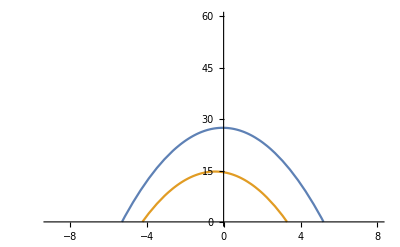

```mathematica
Block[{a=1/2,e=0.98},Plot[{Qs[e,l,a],Qu[e,l,a]},{l,-10,10},PlotRange->{{-9,8},{0,60}}]]
```

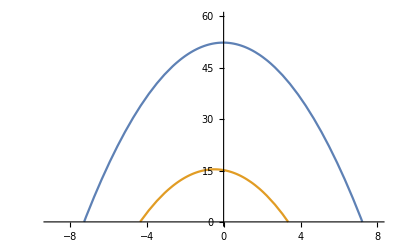

```mathematica
Block[{a=1/2,e=0.99},Plot[{Qs[e,l,a],Qu[e,l,a]},{l,-10,10},PlotRange-> {{-9,8},{0,60}}]]
```

## Figure 9

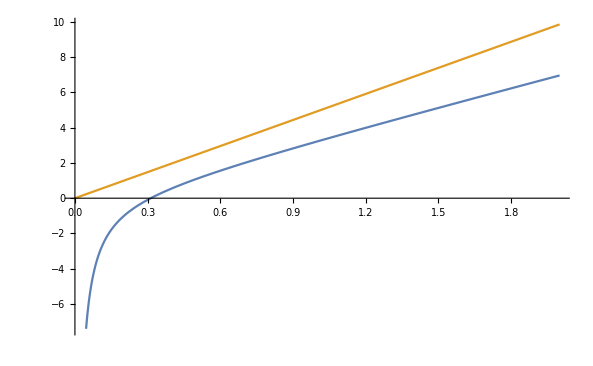

```mathematica
Block[{a=ac[1]-0.01},Plot[{le[e,a],lp[e,a],lu[e,a],ls[e,a]},{e,0,2}]]
```

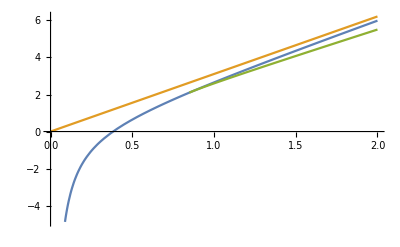

```mathematica
Block[{a=ac[3]},Plot[{le[e,a],lp[e,a],lu[e,a],ls[e,a]},{e,0,2}]]
```

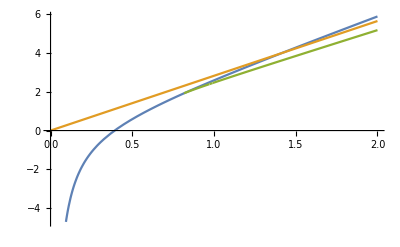

```mathematica
Block[{a=ac[4]},Plot[{le[e,a],lp[e,a],lu[e,a],ls[e,a]},{e,0,2}]]
```

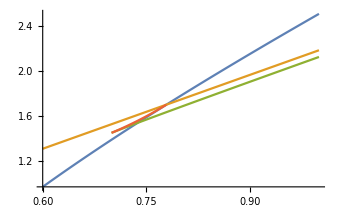

```mathematica
Block[{a=ac[6]},Plot[{le[e,a],lp[e,a],lu[e,a],ls[e,a]},{e,0.6,1}]]
```

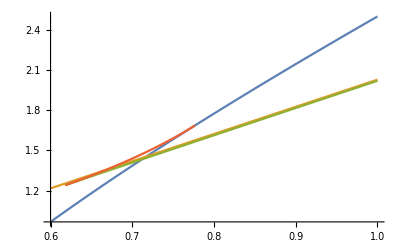

```mathematica
Block[{a=0.9999},Plot[{le[e,a],lp[e,a],lu[e,a],ls[e,a]},{e,0.6,1}]]
```